# Hitting of Cyclones to West Coast North America

Baoxiang Pan
7.10.2017

## Import Lagrangian Detected Cyclone Data

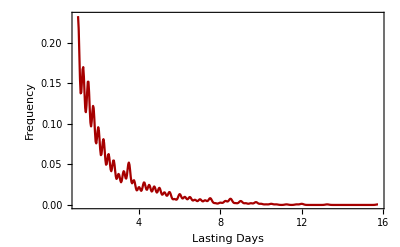

```mathematica
cyclones=Import["/Users/lambda/Documents/Data/Cyclones/ncepstorms_2009.txt","Table"];
data=Table[Select[cyclones,#[[-1]]==i&],{i,Max[Map[#[[-1]]&,cyclones]]}];
length=Map[Length,data]*0.25;
Block[{distribution=SmoothKernelDistribution[length]},
Plot[PDF[distribution, x], {x, 1, Max[length]},
	PlotRange->Full,
	BaseStyle->18,
	Frame->True,
	FrameLabel->{"Lasting Days","Frequency"}]]
```

```mathematica
cyclones=Import["/Users/lambda/Documents/Data/Cyclones/cyclones.txt","Table"][[2;;]];
```

```mathematica
Table[Block[{filename="ncepstorms_19"<>ToString[i]<>".txt"},
	Export[filename,Select[cyclones,#[[3]]==i&],"Table"]],{i,58,99}];
```

```mathematica
Table[Block[{filename="ncepstorms_200"<>ToString[i]<>".txt"},
	Export[filename,Select[cyclones,#[[3]]==i&],"Table"]],{i,0,8}];
```

```mathematica
CycloneSpecify[time_,range_]:=Block[{file="ncepstorms_"<>ToString[time[[1]]]<>".txt",
			lag=3,cyclones,s1,s2,ByPass},
	SetDirectory["/Users/lambda/Documents/Data/Cyclones"];
	cyclones=Import[file,"Table"];
	s1=Select[cyclones,Abs[DateDifference[If[#[[3]]<20,
							DateObject[{2000+#[[3]],#[[4]],#[[5]]},"Day", "Gregorian", -6.],
							DateObject[{1900+#[[3]],#[[4]],#[[5]]},"Day", "Gregorian", -6.]],
							DateObject[time,"Day","Gregorian",-6.]][[1]]]<lag&];
	s2=Table[Select[s1,#[[-1]]==i&],{i,Max[Map[#[[-1]]&,s1]]}];
	ByPass[track_]:=Block[{InOrNot},
	    InOrNot[point_]:=And[point[[1]]>=range[[1,1]],point[[1]]<range[[1,2]],
	                       point[[2]]>=range[[2,1]],point[[2]]<range[[2,2]]];
		Map[InOrNot[{#[[14]],#[[15]]}]&,track]/.List->Or];
	Select[s2,ByPass]]
```

```mathematica
SequentialDetection[date_]:=Block[{pendant=Table[i,{i,2,365,5}]},
	Map[CycloneSpecify[DatePlus[DateObject[date,"Day", "Gregorian", -6.],{#,"Day"}][[1]],
				  {{30,70},{219,251}}]&,pendant]]
```

```mathematica
test2=SequentialDetection[{1967,1,1}];
Export["1967cross.txt",test2,"List"];
```

```mathematica
test3=SequentialDetection[{1968,1,1}];
Export["1968cross.txt",test3,"List"];
```

```mathematica
test4=SequentialDetection[{1969,1,1}];
Export["1969cross.txt",test4,"List"];
```

```mathematica
test5=SequentialDetection[{1966,1,1}];
Export["1966cross.txt",test5,"List"];
```

```mathematica
Dimensions[test[[1]]]
```

{3}

```mathematica
test[[1]]
```

{{{1.,1,58,1,1,0,16,1,1,993.97,4.89,-999.,-999.,45.75,220.76,22,24,0,0,3},{1.25,2,58,1,1,6,15,1,0,990.56,8.27,586.73,-3.41,50.68,217.88,23,26,0,0,3},{1.5,3,58,1,1,12,15,1,0,987.98,9.22,253.91,-2.58,52.54,220.03,24,26,0,0,3},{1.75,4,58,1,1,18,13,1,0,985.38,7.76,247.89,-2.6,54.02,217.24,24,27,0,0,3},{2.,5,58,1,2,0,16,1,0,981.75,17.22,369.59,-3.63,57.32,216.47,25,28,0,0,3},{2.25,6,58,1,2,6,13,1,0,978.47,20.59,493.26,-3.28,59.88,209.48,25,30,0,0,3},{2.5,7,58,1,2,12,13,1,0,980.57,11.09,0.,2.1,59.88,209.48,25,30,0,0,3},{2.75,8,58,1,2,18,14,1,0,982.76,7.13,245.54,2.18,60.95,205.56,25,31,0,0,3},{3.,9,58,1,3,0,9,1,0,986.79,5.62,557.66,4.03,57.49,198.43,23,32,0,1,3}},{{3.75,12,58,1,3,18,16,1,0,986.11,14.4,-999.,-999.,57.65,222.14,26,27,1,0,48},{4.,13,58,1,4,0,17,1,0,987.24,12.94,0.,1.13,57.65,222.14,26,27,0,0,48},{4.25,14,58,1,4,6,17,1,0,986.3,27.15,575.69,-0.94,62.64,225.,28,28,0,0,48},{4.5,15,58,1,4,12,14,1,0,991.,25.49,343.73,4.7,62.45,231.71,29,27,0,1,48}},{{4.75,16,58,1,4,18,13,1,0,991.67,8.67,-999.,-999.,61.88,248.63,32,25,1,0,62},{5.,17,58,1,5,0,13,1,0,991.13,11.8,767.53,-0.54,61.32,263.16,35,24,0,0,62},{5.25,18,58,1,5,6,15,1,0,988.96,13.55,242.49,-2.17,61.51,267.71,36,24,0,0,62},{5.5,19,58,1,5,12,13,1,0,984.41,18.55,354.11,-4.55,59.18,272.12,37,23,0,0,62},{5.75,20,58,1,5,18,13,1,0,979.93,22.04,765.66,-4.48,60.41,285.64,40,24,0,0,62}}}

```mathematica
Dimensions[centers]
```

{3,73,3}

```mathematica
Append[{1,2,3},4]
```

{1,2,3,4}

```mathematica
centers[[1,1]][[1;;2]]
```

{50.4752,232.5}

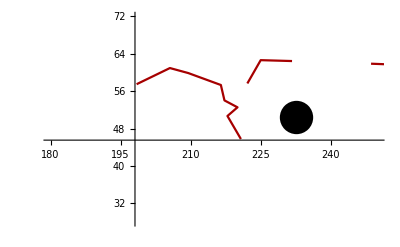
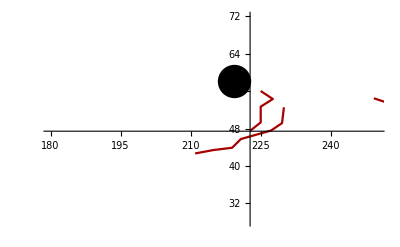
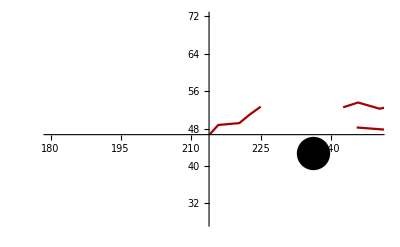
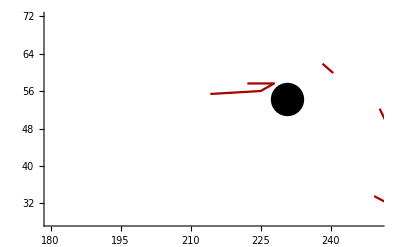
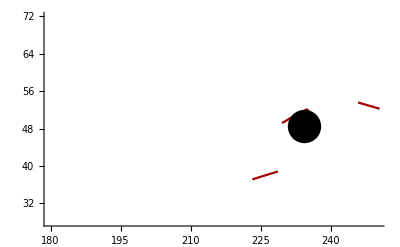
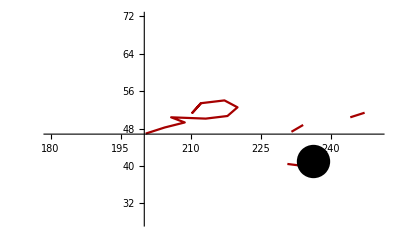
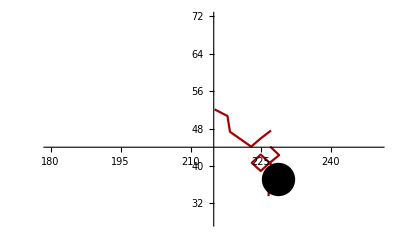
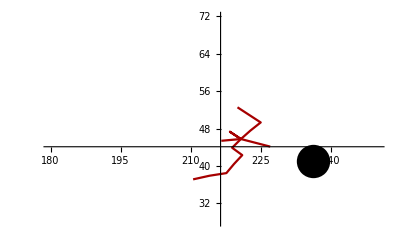

```mathematica
Table[Show[Append[Table[ListLinePlot[Map[{#[[15]],#[[14]]}&,test[[day,i]]]],{i,Length[test[[day]]]}],
		 Graphics[{PointSize[0.06],Point[{centers[[1,day]][[2]],centers[[1,day]][[1]]}]}]],
		 PlotRange->{{180,250},{28,72}}],{day,1,73}]
```

```mathematica
slat=10;
elat=32;
slon=118;
elon=135;
winter=Flatten[Table[{Range[1+i*73,24+i*73],Range[50+i*73,73+i*73]},{i,0,69}]][[1;;-25]];
SetDirectory["/Volumes/lambda/Data/Reanalysis/NCEP/Precipitation"];
file=FileNames["*.nc"][[11;;13]];
lat=Import[file[[1]],{"Datasets","lat"}][[slat;;elat]];
lon=Import[file[[1]],{"Datasets","lon"}][[slon;;elon]];
centers=Table[Block[{p,cp,T=20},
	p=Import[file[[i]],{"Datasets","prate"}];
	p=p[[;;,slat;;elat,slon;;elon]];
	cp=Table[Total[p[[j;;j+T-1,;;,;;]]],{j,1,Length[p]-T+1,T}];
	Map[{lat[[Position[#,Max[#]][[1,1]]]],
		 lon[[Position[#,Max[#]][[1,2]]]],
		 Max[#]}&,cp]],{i,Length[file]}];
```